This notebook has the same formatting as an earlier version of the SCCC Mathematica Tutorial.

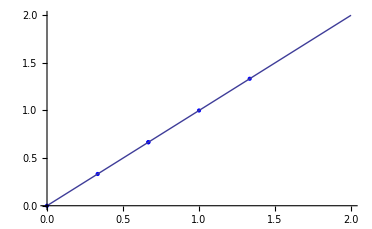

{0,1/3,2/3,2/3,1,4/3,4/3,5/3,2}

{0,1/3,2/3,2/3,1,4/3,4/3,5/3,2}

1.92826

9

4/3

5/3

2

{{a→-3/2,b→11/2,c→-10/3}}

```mathematica
(*To do:*)
(*Define a function that takes a function, low/high limits, and number of partitions and calculates the area*)
CalculateLeftHand[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n}];
(*Get the area*)
ret = 0;
Do[ret = ret+(func[xVars[[index]]]), {index, n}];

Return[N[ret*dx]]
);
CalculateRightHand[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n}];
(*Get the area*)
ret = 0;
Do[ret = ret+(func[xVars[[index+1]]]), {index, n}];

Return[N[ret*dx]]
);
CalculateMidPoint[func_, low_, high_, n_]:= (
dx = (high-low)/n;
offset = dx/2;
xVars = {low+offset};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n}];
(*Get the area*)
ret = 0;
Do[ret = ret+(func[xVars[[index]]]), {index, n}];

Return[N[ret*dx]]
);
CalculateTrapazoid[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[
xVars = Append[xVars, xVars[[index]]+dx];
, {index,n-1}
];
Do[
xVars = Append[xVars, xVars[[index]]+dx];
, {index,n-1}
];

xVars = Sort[xVars];
xVars = Append[xVars, high];
(*Get the area*)
ret = 0;
Do[ret = ret+(func[xVars[[index]]]), {index, Length[xVars]}];

Return[N[ret*(dx/2)]]
);
CalculateSimpsonsRule[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVals = {low};
(*Get each x value*)
Do[
xVals = Append[xVals, xVals[[index]]+dx];
, {index,n}
];

xVars = {};

For[i=1, i<(Length[xVals]-1), i+=2,
xVars = Append[xVars, xVals[[i]]];
xVars = Append[xVars, xVals[[i+1]]];
xVars = Append[xVars, xVals[[i+1]]];
xVars = Append[xVars, xVals[[i+1]]];
xVars = Append[xVars, xVals[[i+1]]];
xVars = Append[xVars, xVals[[i+2]]];
]



(*Get the area*)
ret = 0;
Do[ret = ret+(func[xVars[[index]]]), {index, Length[xVars]}];

Return[N[ret*(dx/3)]]
);

(*Define a function that takes a function, low/high limits, and number of partions and draws the graph with the partitions*)
DrawLeftHand[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n}];
yVals = {};
Do[yVals = Append[yVals, func[xVars[[index]]]], {index,n}];
xyList = {};

Do[(
xyList = Append[xyList, {xVars[[index]], 0}];
xyList = Append[xyList, {xVars[[index]], yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, 0}]), {index, n}];

graph = Plot[func[x], {x, low, high}];
rectanlges = ListPlot[xyList, Joined -> True, Filling->Axis, FillingStyle->Pink, PlotStyle ->{Blue},PlotRange -> All];

Show[{rectanlges,graph}, PlotRange -> All]
);

DrawRightHand[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n}];
yVals = {};
Do[yVals = Append[yVals, func[xVars[[index+1]]]], {index,n}];
xyList = {};

Do[(
xyList = Append[xyList, {xVars[[index]], 0}];
xyList = Append[xyList, {xVars[[index]], yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, 0}]), {index, n}];

graph = Plot[func[x], {x, low, high}];
rectanlges = ListPlot[xyList, Joined -> True, Filling->Axis, FillingStyle->Pink, PlotStyle ->{Blue},PlotRange -> All];

Show[{rectanlges, graph}, PlotRange -> All]
);
DrawMidPoint[func_, low_, high_, n_]:= (
dx = (high-low)/n;
offset = dx/2;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n}];

midVars = {low+offset};
(*Get each x value*)
Do[midVars = Append[midVars, midVars[[index]]+dx], {index,n}];

yVals = {};
Do[yVals = Append[yVals, func[midVars[[index]]]], {index,n}];
xyList = {};

Do[(
xyList = Append[xyList, {xVars[[index]], 0}];
xyList = Append[xyList, {xVars[[index]], yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, 0}]), {index, n}];

graph = Plot[func[x], {x, low, high}];
rectanlges = ListPlot[xyList, Joined -> True, Filling->Axis, FillingStyle->Pink, PlotStyle ->{Blue},PlotRange -> All];

Show[{rectanlges, graph}, PlotRange -> All]
);
DrawTrapezoid[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n}];
yVals = {};
Do[yVals = Append[yVals, func[xVars[[index]]]], {index,n+1}];
xyList = {};

Do[(
xyList = Append[xyList, {xVars[[index]], 0}];
xyList = Append[xyList, {xVars[[index]], yVals[[index]]}];
xyList = Append[xyList, {xVars[[index+1]] , yVals[[index+1]]}];
xyList = Append[xyList, {xVars[[index+1]] , 0}]), {index, n}];

graph = Plot[func[x], {x, low, high}];
rectanlges = ListPlot[xyList, Joined -> True, Filling->Axis, FillingStyle->Pink, PlotStyle ->{Blue},PlotRange -> All];

Show[{rectanlges, graph}, PlotRange -> All]
);
DrawSimpsonsRule[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[
xVars = Append[xVars, xVars[[index]]+dx];
, {index,n}
];
For[i=Length[xVars]-2, i>1, i-=2,
xVars = Append[xVars, xVars[[i]]];
];
xVars = Sort[xVars];

yVals = {};
Do[yVals = Append[yVals, func[xVars[[index]]]], {index,Length[xVars]}];
xyList = {};

Do[
xyList = Append[xyList, {xVars[[index]], yVals[[index]]}];
, {index, n}];




equationList = {};

For[i = 1, i<Length[xVars],i+=3,
(
x1 = xVars[[i]];
x2 = xVars[[i+1]];
x3 = xVars[[i+2]];
y1 = yVals[[i]];
y2 = yVals[[i+1]];
y3 = yVals[[i+1]];

temp = Solve[{y1 == a(x1^2) + b(x1) +c, y2 == a(x2^2) + b(x2) +c,y3 == a(x3^2) + b(x3) +c}, {a,b,c}];


c/.temp[[1]];(*gets the thing*)
)];


graph = Plot[func[x], {x, low, high}];
rectanlges = ListPlot[xyList, PlotStyle ->{Blue}, PlotRange -> Full];

Show[{rectanlges, graph}, PlotRange -> All]

);

f[x_]:=x;

Equation1[x_]:= Sqrt[1+x^2]
Equation2[x_]:=ArcTan[x]
Equation3[x_]:=E^(-x^2)

DrawSimpsonsRule[f,0,2,6]
xVars
yVals


c /.test[[1]]


x1
x2
x3
temp
```